```mathematica
Sum[(-1)^k x^(2k),{k,0,Infinity}]
```

1/(1+x^2)

```mathematica
Sum[(-1)^k x^(2k+1)/(2k+1)!,{k,0,Infinity}]
```

Sin[x]

```mathematica
Sum[(-1)^k x^(2k+1),{k,0,Infinity}]
```

x/(1+x^2)

```mathematica
Sum[x^k,{k,0,Infinity}]
```

1/(1-x)

```mathematica
Sum[x^k/k!,{k,0,Infinity}]
```

ⅇ^x

```mathematica
cs[x_]:=1/(1+x^2)
```

```mathematica
sn[x_]:=x/(1+x^2)
```

```mathematica
ex[x_]:=1/(1-x)
```

```mathematica
Expand@FullSimplify[cs[ x]+I sn[ x]]
```

ⅈ/(ⅈ+x)

```mathematica
Expand@ex[I x]
```

1/(1-ⅈ x)

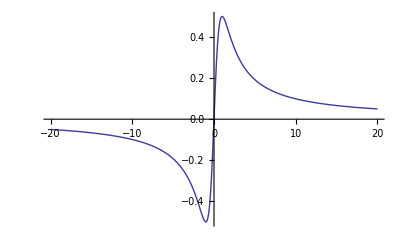

```mathematica
Plot[sn[x],{x,-20,20}]
```

```mathematica
Sum[(-1)^k Binomial[x,2k],{k,0,t}]
```

2^(x/2) Cos[(π x)/4]+(-1)^t Binomial[x,2 (1+t)] HypergeometricPFQ[{1,1+t-x/2,3/2+t-x/2},{3/2+t,2+t},-1]

```mathematica
Sum[(-1)^k Binomial[z,2k+1],{k,0,Floor[x/2]}]
```

(-1)^Floor[x/2] Binomial[z,3+2 Floor[x/2]] HypergeometricPFQ[{1,3/2-z/2+Floor[x/2],2-z/2+Floor[x/2]},{2+Floor[x/2],5/2+Floor[x/2]},-1]+2^(z/2) Sin[(π z)/4]

```mathematica
FullSimplify[2^(x/2) Cos[(π x)/4]+I 2^(x/2) Sin[(π x)/4]]
```

2^(x/2) ⅇ^((ⅈ π x)/4)

```mathematica
Sum[(-1)^k x^(2k)/(2k)!,{k,0,Infinity}]
```

Cos[x]

```mathematica
Sum[Binomial[x,k],{k,0,t}]
```

2^x-Binomial[x,1+t] Hypergeometric2F1[1,1+t-x,2+t,-1]

```mathematica
N[2^(x/2) ⅇ^((ⅈ π x)/4)/.x->3]
```

-2.+2. ⅈ

```mathematica
N[2^x/.x->3I]
```

-0.486994+0.873405 ⅈ

```mathematica
d2[n_,0]:=UnitStep[n-1]
d2[n_,k_]:=d2[n,k]=Sum[d2[Floor[n/j],k-1],{j,2,n}]
ed2[n_]:=Sum[d2[n,k],{k,0,Log2@n}]
csd2[n_]:=Sum[(-1)^k d2[n,2k],{k,0,Log2@n}]
snd2[n_]:=Sum[(-1)^k d2[n,2k+1],{k,0,Log2@n}]
```

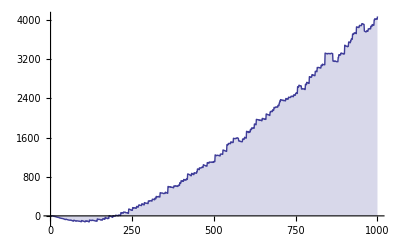

```mathematica
DiscretePlot[csd2[n],{n,1,1000}]
```

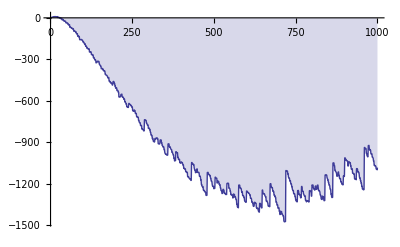

```mathematica
DiscretePlot[snd2[n],{n,1,1000}]
```

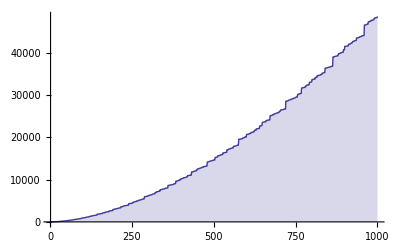

```mathematica
DiscretePlot[ed2[n],{n,1,1000}]
```

```mathematica
Sum[ x^((k-1))/((k)-1)!,{k,0,Infinity}]
```

ⅇ^x

```mathematica
Sum[(-1)^k x^((2k)-1)/((2k)-1)!,{k,0,Infinity}]
```

-Sin[x]

```mathematica
Sum[(-1)^k x^((2k+1)-1)/((2k+1)-1)!,{k,0,Infinity}]
```

Cos[x]

```mathematica
Sum[ Log[x^I]^((k-1))/((k)-1)!,{k,0,Infinity}]
```

x^ⅈ

```mathematica
Sum[(-1)^k Log[x]^((2k)-1)/((2k)-1)!,{k,0,Infinity}]
```

-Sin[Log[x]]

```mathematica
Sum[(-1)^k Log[x]^((2k+1)-1)/((2k+1)-1)!,{k,0,Infinity}]
```

Cos[Log[x]]

```mathematica
FullSimplify[Cos[Log[x]]+I Sin[Log[x]]]
```

x^ⅈ

```mathematica
Sum[ Binomial[z,k],{k,0,Infinity}]
```

2^z

```mathematica
Sum[ (-1)^k Binomial[z,2k],{k,0,Infinity}]
```

2^(z/2) Cos[(π z)/4]

```mathematica
Sum[ (-1)^k Binomial[z,2k+1],{k,0,Infinity}]
```

2^(z/2) Sin[(π z)/4]

```mathematica
Sum[ Binomial[z,k],{k,0,x}]
```

2^z-Binomial[z,1+x] Hypergeometric2F1[1,1+x-z,2+x,-1]

```mathematica
Sum[ (-1)^k Binomial[z,2k],{k,0,x}]
```

2^(z/2) Cos[(π z)/4]+(-1)^x Binomial[z,2 (1+x)] HypergeometricPFQ[{1,1+x-z/2,3/2+x-z/2},{3/2+x,2+x},-1]

```mathematica
Sum[ (-1)^k Binomial[z,2k],{k,0,Floor[x/2]}]
```

2^(z/2) Cos[(π z)/4]+(-1)^Floor[x/2] Binomial[z,2 (1+Floor[x/2])] HypergeometricPFQ[{1,1-z/2+Floor[x/2],3/2-z/2+Floor[x/2]},{3/2+Floor[x/2],2+Floor[x/2]},-1]

```mathematica
Sum[ (-1)^k Binomial[z,2k+1],{k,0,Floor[x/2]}]
```

(-1)^Floor[x/2] Binomial[z,3+2 Floor[x/2]] HypergeometricPFQ[{1,3/2-z/2+Floor[x/2],2-z/2+Floor[x/2]},{2+Floor[x/2],5/2+Floor[x/2]},-1]+2^(z/2) Sin[(π z)/4]

```mathematica
FullSimplify[2^(x/2) Cos[(π x)/4]+I 2^(x/2) Sin[(π x)/4]]
```

```mathematica
Sum[z^k/k!,{k,0,Infinity}]
```

ⅇ^z

```mathematica
Sum[ z^k/k!,{k,0,x}]
```

(ⅇ^z Gamma[1+x,z])/(x!)

```mathematica
Sum[(-1)^k x^(2k)/(2k)!,{k,0,Infinity}]
```

Cos[x]

```mathematica
Sum[(-1)^k z^((2k))/((2k))!,{k,0,Floor[x/2]}]
```

Cos[z]+1/((2 (1+Floor[x/2]))!)(-1)^Floor[x/2] z^(2+2 Floor[x/2]) HypergeometricPFQ[{1},{3/2+Floor[x/2],2+Floor[x/2]},-z^2/4]

```mathematica
Sum[(-1)^k x^((2k+1))/((2k+1))!,{k,0,Infinity}]
```

Sin[x]

```mathematica
Sum[(-1)^k z^((2k+1))/((2k+1))!,{k,0,Floor[x/2]}]
```

1/((3+2 Floor[x/2])!)(-1)^Floor[x/2] z^(3+2 Floor[x/2]) HypergeometricPFQ[{1},{2+Floor[x/2],5/2+Floor[x/2]},-z^2/4]+Sin[z]

```mathematica
Sum[ (Log[t]^(k-1))/(k-1)!,{k,0,Infinity}]
```

t^z z

```mathematica
Integrate[t^z z,{t,1,x}]
```

ConditionalExpression[((-1+x^(1+z)) z)/(1+z),Re[x]≥0||x∉Reals]

```mathematica
Sum[(-1)^k Log[x]^((2k)-1)/((2k)-1)!,{k,0,Infinity}]
```

-Sin[Log[x]]

```mathematica
Integrate[-Sin[Log[x]],{x,1,z}]
```

ConditionalExpression[1/2 (-1+z Cos[Log[z]]-z Sin[Log[z]]),Re[z]≥0||z∉Reals]

```mathematica
Sum[(-1)^k Log[x]^((2k+1)-1)/((2k+1)-1)!,{k,0,Infinity}]
```

Cos[Log[x]]

```mathematica
Integrate[Cos[Log[x]],{x,1,z}]
```

ConditionalExpression[-1/2+1/2 z (Cos[Log[z]]+Sin[Log[z]]),Re[z]≥0||z∉Reals]

```mathematica
Sum[z^k,{k,0,x}]
```

(-1+z^(1+x))/(-1+z)

```mathematica
FullSimplify[Sum[(-1)^(k) z^(2k),{k,0,Floor[x/2]}],Element[x,Integers]]
```

(1+(-1)^Floor[x/2] z^(2+2 Floor[x/2]))/(1+z^2)

```mathematica
FullSimplify[FullSimplify@Expand@Sum[(-1)^k z^(2k+1),{k,0,Floor[x/2]}],Element[x,Integers]]
```

(z+(-1)^Floor[x/2] z^(3+2 Floor[x/2]))/(1+z^2)

```mathematica
Sum[pex[z,k],{k,0,Infinity}]
Sum[ (-1)^k pex[z,2k],{k,0,Infinity}]
Sum[ (-1)^k pex[z,2k+1],{k,0,Infinity}]
```

```mathematica
Sum[ pex[z,k],{k,0,Infinity}]
```

HypergeometricPFQ[{z},{},1]

```mathematica
Sum[ (-1)^k pex[z,2k],{k,0,Infinity}]
```

2^(-z/2) Cos[(π z)/4]

```mathematica
Sum[(-1)^k pex[z,2k],{k,0,Infinity}]
```

2^(-z/2) Cos[(π z)/4]

```mathematica
Sum[ (-1)^k pex[z,2k+1],{k,0,Infinity}]
```

2^(-z/2) Sin[(π z)/4]

```mathematica
FullSimplify@Sum[pex[z,k],{k,0,x}]
```

Gamma[1+x+z]/(Gamma[1+x] Gamma[1+z])

```mathematica
Sum[ (-1)^k pex[z,2k],{k,0,Floor[x/2]}]
```

2^(-z/2) Cos[(π z)/4]+((-1)^Floor[x/2] Gamma[2+z+2 Floor[x/2]] HypergeometricPFQ[{1,1+z/2+Floor[x/2],3/2+z/2+Floor[x/2]},{3/2+Floor[x/2],2+Floor[x/2]},-1])/(Gamma[z] Gamma[3+2 Floor[x/2]])

```mathematica
FullSimplify@Expand@Sum[ (-1)^k pex[z,2k+1],{k,0,Floor[x/2]}]
```

((-1)^Floor[x/2] Gamma[3+z+2 Floor[x/2]] HypergeometricPFQ[{1,3/2+z/2+Floor[x/2],2+z/2+Floor[x/2]},{2+Floor[x/2],5/2+Floor[x/2]},-1])/(Gamma[z] Gamma[4+2 Floor[x/2]])+2^(-z/2) Sin[(π z)/4]

```mathematica
N[Gamma[1+x+z]/(Gamma[1+x] Gamma[1+z])/.x->10/.z->I]
```

-1.61604+0.855131 ⅈ

```mathematica
FullSimplify[Sum[ (-1)^-k Gamma[k,0,-Log[z]]/Gamma[k],{k,0,Infinity}],Element[z,Integers]]
```

∑_(k=0)^∞ ((-1)^-k Gamma[k,0,-Log[z]])/Gamma[k]

```mathematica
FullSimplify@Integrate[E^-Log[j] Log[j]^(k-1)/(k-1)!,{j,1,x}]
```

ConditionalExpression[Log[x]^k/Gamma[1+k],(Re[x]≥0||x∉Reals)&&Re[k]>0]

```mathematica
Sum[Log[z]^k/Gamma[1+k],{k,0,Infinity}]
```

z

```mathematica
Sum[(-1)^k Log[z]^(2k)/((2k)!),{k,0,Infinity}]
```

Cos[Log[z]]

```mathematica
Sum[(-1)^k Log[z]^(2k+1)/((2k+1)!),{k,0,Infinity}]
```

Sin[Log[z]]

```mathematica
N[Cos[Log[z]]+I Sin[Log[z]]/.z->3]
```

0.454832+0.890577 ⅈ

```mathematica
N[3^I]
```

0.454832+0.890577 ⅈ

```mathematica
Integrate[(1/j)(1/Log[j]-1/(j Log[j])),{j,1,x}]
```

ConditionalExpression[EulerGamma+Gamma[0,Log[x]]+Log[Log[x]],Im[x]≠0||Re[x]≥0]

```mathematica
FullSimplify[EulerGamma+Gamma[0,Log[x]]+Log[Log[x]]]/.x->10.
```

1.44364

```mathematica
FullSimplify[Gamma[0,Log[x]]]/.x->10000.
```

9.87515×10^-6

```mathematica
D[LaguerreL[z,-Log[x]],z]/.z->0/.x->10.
```

1.44364

```mathematica
t^Log[j] Log[j]^(k-1)/(k-1)!/.t->E^-1
```

Log[j]^(-1+k)/(j (-1+k)!)

```mathematica
FullSimplify@Integrate[Log[j]^(-1+k)/(j (-1+k)!),{j,1,x}]
```

ConditionalExpression[Log[x]^k/Gamma[1+k],(Re[x]≥0||x∉Reals)&&Re[k]>0]

```mathematica
D[Log[x]^k/Gamma[1+k],k]/.k->0
```

EulerGamma+Log[Log[x]]

```mathematica
D[x^k/(k!),k]/.k->0
```

EulerGamma+Log[x]

```mathematica
Clear[kk]
kk[n_]:=kk[n]=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
pre[n_]:=Sum[kk[j]/j,{j,1,n}]
```

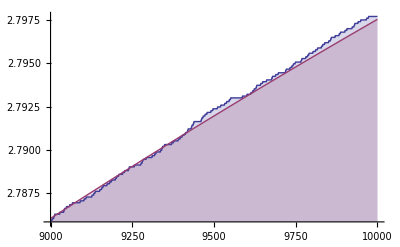

```mathematica
DiscretePlot[{pre[n],Log[Log[n]]+EulerGamma},{n,9000,10000}]
```

```mathematica
1/j+1/2/j^2+1/3/j^3+1/4/j^4/.j->7
```

4441/28812

```mathematica
Clear[dc]
dc[n_,0]:=UnitStep[n-1]
dc[n_,k_]:=dc[n,k]=Sum[(1/j)dc[Floor[n/j],k-1],{j,2,n}]
dz[n_,z_]:=Sum[binomial[z,k]dc[n,k],{k,0,Log2@n}]
```

```mathematica
N@Table[dc[10000,k],{k,0,Log2@10000}]
```

{1.,8.78761,34.9535,83.1143,131.372,145.108,114.572,64.9853,26.2128,7.32402,1.35067,0.155159,0.0108236,0.00012207}

```mathematica
N@Table[Log[10000]^k/(k!),{k,0,Log2@10000}]
```

{1.,9.21034,42.4152,130.219,299.841,552.328,847.855,1115.58,1284.35,1314.37,1210.58,1013.62,777.985,551.193}

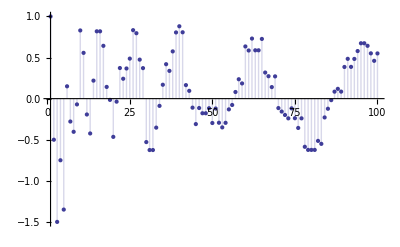

```mathematica
DiscretePlot[dz[n,-3],{n,1,100}]
```

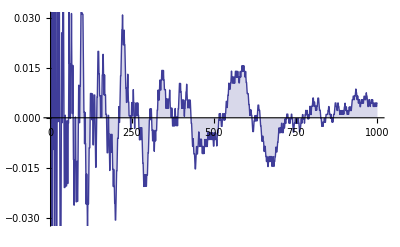

```mathematica
DiscretePlot[{dz[n,-1]},{n,1,1000}]
```

```mathematica
binomial[z_,k_]:=binomial[z,k]=Product[z-j,{j,0,k-1}]/k!
zetaHurwitz[n_,s_,y_,0]:=UnitStep[n-1]
zetaHurwitz[n_,s_,y_,1]:=zetaHurwitz[n,s,y,1]=HarmonicNumber[Floor[n],s]-HarmonicNumber[y,s]
zetaHurwitz[n_,s_,y_,2]:=zetaHurwitz[n,s,y,2]=Sum[(m^(-2s))+2(m^-s) (zetaHurwitz[Floor[n/m],s,m,1]),{m,y+1,Floor[n^(1/2)]}]
zetaHurwitz[n_,s_,y_,k_]:=zetaHurwitz[n,s,y,k]=Sum[(m^(-s k))+k(m^(-s(k-1))) zetaHurwitz[Floor[n/(m^(k-1))],s,m,1]+Sum[binomial[k,j] (m^-s)^j zetaHurwitz[Floor[n/(m^j)],s,m,k-j],{j,1,k-2}],{m,y+1,Floor[n^(1/k)]}]

zeta[n_,s_,1]:=Expand@Sum[binomial[1,k]zetaHurwitz[n,s,1,k],{k,0,1}]
zeta[n_,s_,z_]:=Expand@Sum[binomial[z,k]zetaHurwitz[n,s,1,k],{k,0,Log2@n}]
```

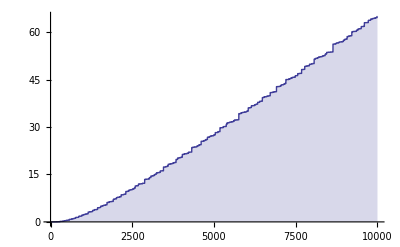

```mathematica
DiscretePlot[zetaHurwitz[n,1,1,7],{n,1,10000}]
```

```mathematica
Log[Log[10000.]]
```

2.22033

```mathematica
HarmonicNumber[10000.]
```

9.78761

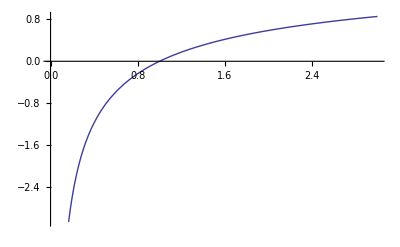

```mathematica
Plot[Gamma[0,Log[x]]+Log[Log[x]]+EulerGamma,{x,0,3}]
```

```mathematica
Limit[LogIntegral[100^(1-s)]-Log[Log[100^(1-s)]]-EulerGamma,s->1]
```

-ⅈ π

```mathematica
bal[n_,x_,s_]:=Sum[(x^(k(1-s))-1)/k,{k,1,Log[x,n]}]
```

```mathematica
bal[100.,1.00001,1-.00001I]
```

-5.3019×10^-10+0.0000460517 ⅈ

```mathematica
N@Log[Log[100^ZetaZero[1]]]
```

1.17157+0.776278 ⅈ

```mathematica
N[Log[ZetaZero[2]Log[100]]+Log[ZetaZero[-2]Log[100]]]
```

9.14607+0. ⅈ

```mathematica
Integrate[(1/j) Log[j]^k/(k!),{j,1,x}]
```

ConditionalExpression[Log[x]^(1+k)/((1+k) k!),(Re[x]≥0||x∉Reals)&&Re[k]>-1]

```mathematica
Clear[dd2, do2]
do2[n_,0]:=UnitStep[n-1]
do2[n_,k_]:=do2[n,k]=Sum[ do2[Floor[n/j],k-1],{j,2,n}]
do2a[n_,k_]:=do2[n,k]-do2[n-1,k]
dd2[n_,0]:=UnitStep[n-1]
dd2[n_,k_]:=dd2[n,k]=Sum[1/j dd2[Floor[n/j],k-1],{j,2,n}]
dd2a[n_,k_]:=dd2[n,k]-dd2[n-1,k]
```

```mathematica
Table[dd2a[j,3],{j,1,20}]
```

{0,0,0,0,0,0,0,1/8,0,0,0,1/4,0,0,0,3/16,0,1/6,0,3/20}

```mathematica
Table[dd2[j,2],{j,1,20}]
```

{0,0,0,1/4,1/4,7/12,7/12,5/6,17/18,103/90,103/90,133/90,133/90,1021/630,221/126,1957/1008,1957/1008,727/336,727/336,3971/1680}